```mathematica
save[name_]:=Export[NotebookDirectory[]<>"../../pages/posts/img/"<>name<>".png",%,ImageResolution->200,Background->None]
```

```mathematica
eqns[β_:β,γ_:γ]:={s'[t]==-β s[t]i[t],i'[t]==β s[t]i[t]-γ i[t],r'[t]==γ i[t]}
init={s[0]==99,i[0]==1,r[0]==0};
```

```mathematica
pars={{.01,.3},{.02,.3},{.01,.5}};
sol=Table[NDSolve[{eqns@@par,init},{s,i,r},{t,0,20}],{par,pars}];
```

```mathematica
labels=Row/@({"β = "<>ToString[#1]<>", γ = "<>ToString[#2]}&@@@pars);
```

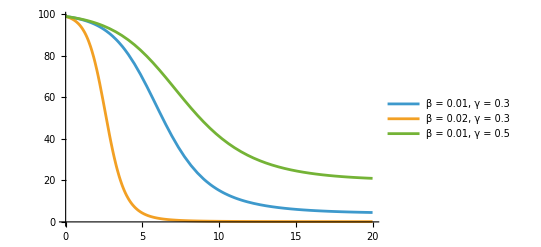

D:\11\website\resources\mm\../../pages/posts/img/sirs.png

```mathematica
Plot[Evaluate[s[t]/.sol],{t,0,20},PlotLegends->labels]
save["sirs"]
```

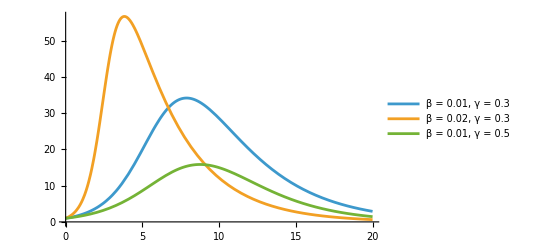

D:\11\website\resources\mm\../../pages/posts/img/siri.png

```mathematica
Plot[Evaluate[i[t]/.sol],{t,0,20},PlotLegends->labels]
save["siri"]
```

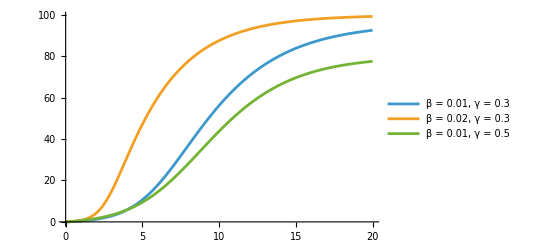

D:\11\website\resources\mm\../../pages/posts/img/sirr.png

```mathematica
Plot[Evaluate[r[t]/.sol],{t,0,20},PlotLegends->labels]
save["sirr"]
```

```mathematica
rawConfirmed=Import["C:\\Users\\Naman Taggar\\Downloads\\time_series_covid19_confirmed_global.csv","CSV"];
rawDeaths=Import["C:\\Users\\Naman Taggar\\Downloads\\time_series_covid19_deaths_global.csv","CSV"];
rawRecovered=Import["C:\\Users\\Naman Taggar\\Downloads\\time_series_covid19_recovered_global.csv","CSV"];
```

```mathematica
getTS[raw_,country_]:=Module[{row,dates,vals},row=SelectFirst[Rest[raw],#[[2]]==country&];
dates=raw[[1,5;;]];
vals=row[[5;;]];
TimeSeries[Transpose[{dates,vals}]]];
```

```mathematica
rawseries[con_]:={getTS[rawConfirmed,con],getTS[rawRecovered,con],getTS[rawDeaths,con]}
```

```mathematica
infection[con_]:=infection[con]=Module[
{rs=rawseries[con]},
TimeSeries[Transpose[{rs[[1]]["Times"],rs[[1]]["Values"]-rs[[2]]["Values"]-rs[[3]]["Values"]}]]
]
```

```mathematica
india=TimeSeriesWindow[#,{"21 Jan 2020","01 Aug 2021"}]&@infection["India"]
```

TimeSeries[…]

```mathematica
sa=TimeSeriesWindow[#,{"21 Jan 2020","01 Aug 2021"}]&@infection["South Africa"]
```

TimeSeries[…]

```mathematica
serbia=TimeSeriesWindow[#,{"21 Jan 2020","01 Aug 2021"}]&@infection["Serbia"]
```

TimeSeries[…]

```mathematica
indonesia=TimeSeriesWindow[#,{"21 Jan 2020","01 Aug 2021"}]&@infection["Indonesia"]
```

TimeSeries[…]

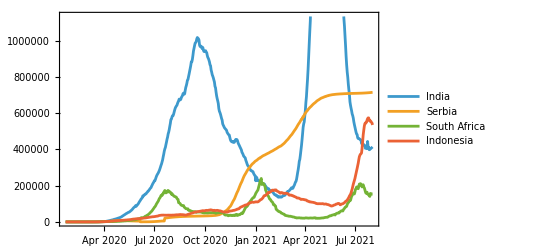

D:\11\website\resources\mm\../../pages/posts/img/countries.png

```mathematica
DateListPlot[{india,serbia,sa,indonesia},
PlotLegends->{"India","Serbia","South Africa","Indonesia"}]
save["countries"]
```

```mathematica
india["Values"]//Length
```

558

```mathematica
n=1.4 10^7
```

1.4×10^7

```mathematica
tmax=558
```

558

```mathematica
eqns[β,γ]
```

{s'[t]==-β i[t] s[t],i'[t]==-γ i[t]+β i[t] s[t],r'[t]==γ i[t]}

```mathematica
ClearAll[model]
model[β_?NumericQ,γ_?NumericQ]:=model[β,γ]=NDSolveValue[{eqns[β,γ],{s[0]==1,i[0]==10/n,r[0]==0}},i,{t,0,tmax}]
```

```mathematica
inf=Transpose[{Range[558],indonesia["Values"]/n}];
```

```mathematica
fit=Quiet@FindFit[inf,model[β,γ][t],{{β,.1},{γ,.15}},t]
```

{β→0.000507692,γ→-0.0190771}

```mathematica
infr=i/.NDSolve[{
eqns[β,γ]/.fit,
{s[0]==1,i[0]==1/n,r[0]==0}},
{s,i,r},{t,0,tmax}]
```

{InterpolatingFunction[…]}

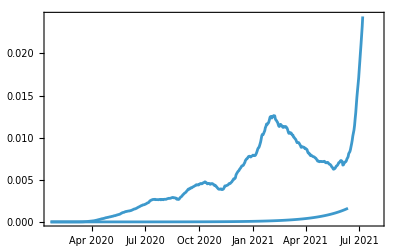

```mathematica
Show[
DateListPlot[Transpose[{indonesia["Dates"],indonesia["Values"]/n}]],
DateListPlot[Transpose[{indonesia["Dates"],infr[[1]]/@Range[558]}]]
]
```

```mathematica
eeqns[β_,γ_,λ1_,λ2_,a1_,a2_,a3_,b1_,b2_,b3_,c1_,c2_,c3_,p1_,p2_]:=
{s'[t]==-β s[t]i[t]+(λ1 t+λ2)/n,
i'[t]==β s[t]i[t]-γ i[t]+(a1 b1 Cos[b1 t+c1]+a2 b2 Cos[b2 t+c2]+a3 b3 Cos[b3 t+c3])/n,
r'[t]==γ i[t]+(p1 t+p2)/n}
```

```mathematica
model[β_?NumericQ,γ_?NumericQ,λ1_?NumericQ,λ2_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,b1_?NumericQ,b2_?NumericQ,b3_?NumericQ,c1_?NumericQ,c2_?NumericQ,c3_?NumericQ,p1_?NumericQ,p2_?NumericQ]:=model[β,γ,λ1,λ2,a1,a2,a3,b1,b2,b3,c1,c2,c3,p1,p2]=Module[{sol},sol=NDSolveValue[{eqns[β,γ,λ1,λ2,a1,a2,a3,b1,b2,b3,c1,c2,c3,p1,p2],{s[0]==1,i[0]==10/n,r[0]==0}},i,{t,0,386}];
sol]
```

```mathematica
inf=Transpose[{Range[Length[india["Values"]]],india["Values"]}];
```

```mathematica
fit=FindFit[{#[[1]],#[[2]]/n}&/@inf,model[β,γ,λ1,λ2,a1,a2,a3,b1,b2,b3,c1,c2,c3,p1,p2][t],{{β,0.5},{γ,0.1},{λ1,0},{λ2,0},{a1,100},{a2,100},{a3,100},{b1,0.01},{b2,0.05},{b3,0.02},{c1,0},{c2,0},{c3,0},{p1,0},{p2,0}},t,PrecisionGoal->4,AccuracyGoal->4]
```

InterpolatingFunction::dmval: Input value {179.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {181.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
infr=i/.NDSolve[{
eqns[β,γ,λ1,λ2,a1,a2,a3,b1,b2,b3,c1,c2,c3,p1,p2]/.fit,
{s[0]==1.4 10^9,i[0]==10,r[0]==0}},
{s,i,r},{t,0,700}]
```

{InterpolatingFunction[…]}

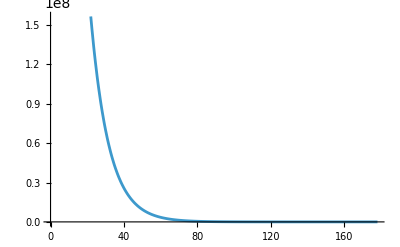

```mathematica
Plot[infr[[1]][t],{t,0,178}]
```

```mathematica
model[β_?NumericQ,γ_?NumericQ]:=model[β,γ]=NDSolveValue[{eqns[β,γ],init},i,{t,0,386}];
```

```mathematica
fi=Quiet@FindFit[inf,{model[β,γ][t],β>0,γ>0},{β,γ},t]
```

{β→6.62107,γ→1.00002}

{{i→InterpolatingFunction[…]}}

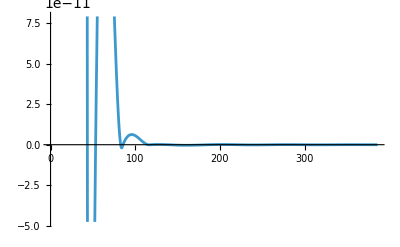

```mathematica
sol=NDSolve[{eqns[β,γ]/.fi,{s[0]==n,i[0]==10,r[0]==0}},i,{t,0,386}]
Plot[i[t]/.sol,{t,0,386}]
```